```mathematica
L[a_, x_]:=Piecewise[{{Sinc[Pi*x]Sinc[Pi*x/a], -a<x<a}},0]
```

```mathematica
Plot3D[L[3,x]*L[3,y],{x,-4,4},{y,-4,4},WorkingPrecision->20,PlotRange->Full,MaxRecursion->10]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-y^2]*Exp[-x^2],{x,-4,4},{y,-4,4},PlotRange->Full]
```

-Graphics3D-

```mathematica
Exp[-y^2]*Exp[-x^2]
```

ⅇ^(-x^2-y^2)

```mathematica
Exp[-(x^2+y^2)]
```

ⅇ^(-x^2-y^2)

```mathematica
Simplify[L[3,x]*L[3,y]]
```

Piecewise[{{Sinc[(π x)/3] Sinc[π x] Sinc[(π y)/3] Sinc[π y], -3<x<3&&-3<y<3}, {0, True}}]

```mathematica
Simplify[Expand[L[3,Sqrt[x^2+y^2]]]]
```

Piecewise[{{Sinc[1/3 π √(x^2+y^2)] Sinc[π √(x^2+y^2)], -3<√(x^2+y^2)<3}, {0, True}}]

```mathematica
Plot3D[L[3,Sqrt[x^2+(y)^2]],{x,-4,4},{y,-4,4},PlotRange->Full,WorkingPrecision->10,MaxRecursion->10,PlotPoints->25]
```

-Graphics3D-

```mathematica
b[w_] = FourierTransform[Piecewise[{{1,-1<x<1}},0],x,w]
```

(√(2/π) Sin[w])/w

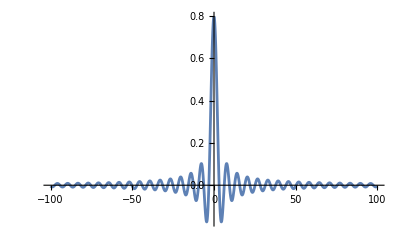

```mathematica
Plot[b[w],{w,-100, 100},PlotRange->Full]
```

```mathematica
NIntegrate[L[20,x],{x,-Infinity,Infinity}]
```

1.00001

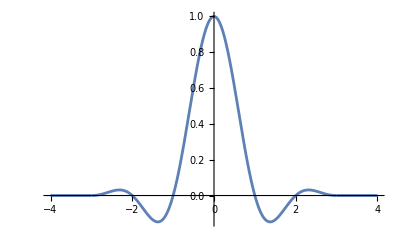

```mathematica
Plot[L[3,x],{x,-4,4},PlotRange->Full]
```

```mathematica
T[x_]:=L[3,x-3]+L[3,x-2]+L[3,x-1]+L[3,x]+L[3,x+1]+L[3,x+2]+L[3,x+3]
```

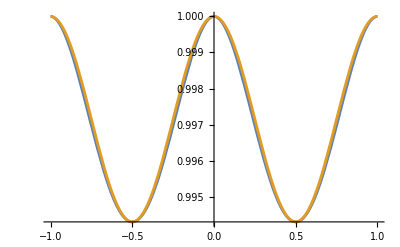

```mathematica
Plot[{T[x],1-((1-0.9943)/2)(Sin[2Pi*(x-0.25)]+1)},{x,-1,1}]
```

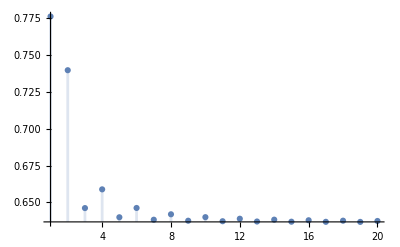

```mathematica
DiscretePlot[NIntegrate[L[a,Sqrt[x^2+y^2]],{x,-a,a},{y,-a,a}],{a,20},PlotRange->Full]
```

```mathematica
NIntegrate[L[3,Sqrt[x^2+y^2]],{x,-3,3},{y,-3,3}]
```

0.646204

```mathematica
L2[a_,x_,y_]:=L[a,Sqrt[x*x+y*y]]
```

```mathematica
L2T[x_,y_]:=L2[3,x,y]
```

```mathematica
T2a[x_,y_]:=L2T[x-3,y]+L2T[x-2,y]+L2T[x-1,y]+L2T[x,y]+L2T[x+1,y]+L2T[x+2,y]+L2T[x+3,y]
```

```mathematica
T2[x_,y_]:=T2a[x,y-3]+T2a[x,y-2]+T2a[x,y-1]+T2a[x,y]+T2a[x,y+1]+T2a[x,y+2]+T2a[x,y+3]
```

```mathematica
N[T2[0,0.5]]
```

0.649879